Helper tools

```mathematica
ClearAll["Global`*"]
basepath="/Users/basavyr/Documents/Work/Repos/mathematica-useful-algorithms/Physics/Elliptic-Functions-New-Boson/Figures/Frequencies";
export[object_,name_,format_]:=Export[StringTemplate["``/``.``"][basepath,name,format],object, ImageResolution->1500];
linspace[a_,b_,n_]:=Table[N[q],{q,a,b,(b-a)/(n-1)}];
```

Numerical values

```mathematica
MOIfit1={91,9,51};
MOIfit2={13.53,101.76,52.94};
MOIfit3={89,12,48};
thetadegfit1=-119;
thetadegfit2=140;
thetadegfit3=-71;
oddspin=5.5;
Ak[mois_]:=N[1/(2*#)]&/@mois;
rad[thetadeg_]:=N[thetadeg*π/180];
j1[thetadeg_]:=oddspin*Cos[rad[thetadeg]];
j2[thetadeg_]:=oddspin*Sin[rad[thetadeg]];
```

Analytical Formulas

```mathematica
A[I_,thetadeg_,mois_]:=Ak[mois][[2]](1-j2[thetadeg]/I)-Ak[mois][[1]];
u[I_,thetadeg_,mois_]:=(Ak[mois][[3]]-Ak[mois][[1]])/A[I,thetadeg,mois];
v0[I_,thetadeg_,mois_]:=-(Ak[mois][[1]]*j1[thetadeg])/A[I,thetadeg,mois];
```

## The wobbling frequency evaluated for 135Pr

Omega ω

```mathematica
A21[I_,thetadeg_,mois_]:=(Ak[mois][[2]]-Ak[mois][[1]]-(Ak[mois][[2]]*j2[thetadeg])/I);
omega[I_,thetadeg_,mois_]:=(((2I+1)*A21[I,thetadeg,mois]+2*Ak[mois][[1]]*j1[thetadeg])*((2I+1)*(Ak[mois][[3]]-Ak[mois][[1]])+2*Ak[mois][[1]]*j1[thetadeg])-(Ak[mois][[3]]-Ak[mois][[1]])*A21[I,thetadeg,mois])^(1/2);
```

Numerical values (tabulated

```mathematica
spinvalues=linspace[7.5,40.5,5];
omegavaluesfit1=Table[{omega[spin,thetadegfit1,MOIfit1],omega[spin,thetadegfit1+180,MOIfit1]},{spin,spinvalues}];
omegavaluesfit2=Table[{omega[spin,thetadegfit2,MOIfit2],omega[spin,thetadegfit2+180,MOIfit2]},{spin,spinvalues}];
omegavaluesfit3=Table[{omega[spin,thetadegfit3,MOIfit3],omega[spin,thetadegfit3+180,MOIfit3]},{spin,spinvalues}];
numericalvalues=Table[{spinvalues[[i]],omegavaluesfit1[[i,1]],omegavaluesfit1[[i,2]],omegavaluesfit2[[i,1]],omegavaluesfit2[[i,2]],omegavaluesfit3[[i,1]],omegavaluesfit3[[i,2]]},{i,1,Length[spinvalues]}];
header={"I","ω1","ω1'","ω2","ω2'","ω3","ω3'"};
numericalvalues=Insert[numericalvalues,header,1];
```

```mathematica
Grid[numericalvalues,Frame->All]
```

I | ω1 | ω1' | ω2 | ω2' | ω3 | ω3'
7.5 | 0.229851 | 0.159683 | 0.803892 | 0.142569 | 0.319873 | 0.0729018
15.75 | 0.487584 | 0.432399 | 1.29345 | 0.635287 | 0.536954 | 0.309143
24. | 0.734667 | 0.682297 | 1.78325 | 1.12564 | 0.754136 | 0.529363
32.25 | 0.979343 | 0.928154 | 2.2731 | 1.61573 | 0.971268 | 0.747743
40.5 | 1.22308 | 1.17254 | 2.76297 | 2.10572 | 1.18837 | 0.965518

Graphical representations for ω

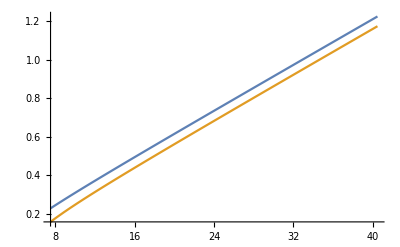

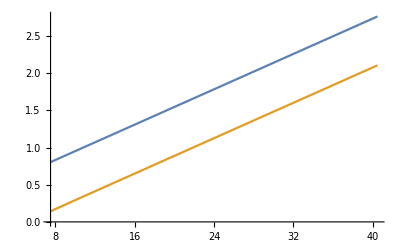

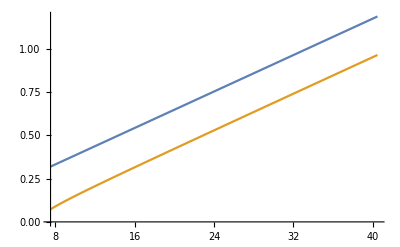

```mathematica
Plot[{omega[x,thetadegfit1,MOIfit1],omega[x,thetadegfit1+180,MOIfit1]},{x,7.5,40.5}]
Plot[{omega[x,thetadegfit2,MOIfit2],omega[x,thetadegfit2+180,MOIfit2]},{x,7.5,40.5}]
Plot[{omega[x,thetadegfit3,MOIfit3],omega[x,thetadegfit3+180,MOIfit3]},{x,7.5,40.5}]
```